```mathematica
OS="win";(*or linux*)
Needs["EDA`"];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum=11623];
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
(*6->HV, SF1->25, SF2->26,U->27,D->28,U+D->,Monitor->30,TotN->32,Fill->31,RF->-1*)
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: 11623

```mathematica
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum,10,6],"\\",IntegerString[runNum,10,6],"_Meta3.edm"],metaStructure2];
Print["# Cycles = ",maxCy=data[[-1]][[2]]];
aCy=Round[(maxCy-4)/4];
mult=.000003902;
meanhgfr=Mean[{data[[100]][[-1]],data[[100+1]][[-1]],data[[100+2]][[-1]],data[[100+3]][[-1]]}];
fita[ftdata_,i_]:=(
nlm=NonlinearModelFit[ftdata,(-bb Cos[((xx-cc)*2Pi)/(180*mult)]),{{bb,.8},{cc,Mean[ftdata[[;;,1]]]}},xx];
Return[{Mean[{data[[i]][[-1]],data[[i+1]][[-1]],data[[i+2]][[-1]],data[[i+3]][[-1]]}]-meanhgfr,nlm["AdjustedRSquared"]}];
);
fitsa=Table[{0,0},{k,1,aCy}];
pts=Table[{0,0},{k,1,4}];
aerr=Table[0,{k,1,maxCy-3}];
ptpts={};
For[i=1,i≤maxCy-4,i+=4,
For[j=0,j≤3,j++,
pts[[j+1]]={N[data[[i+j]][[-1]]/data[[i+j]][[-5]]],N[((data[[i+j]][[27]]-data[[i+j]][[28]])/(data[[i+j]][[27]]+data[[i+j]][[28]]))]};
aerr[[i+j]]=(Sqrt[data[[i+j]][[27]]]+Sqrt[data[[i+j]][[28]]])*Sqrt[2]/(data[[i+j]][[27]]+data[[i+j]][[28]]);
];
fitsa[[Round[((i-1)/4)+1]]]=fita[pts,i];
AppendTo[ptpts,pts];
];
```

# Cycles = 224.

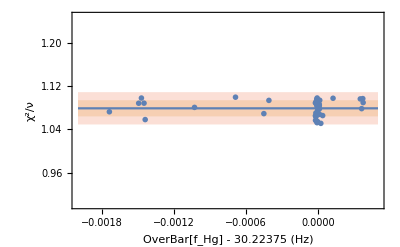

```mathematica
slfitsa=Select[fitsa,((*(#[[1]]<-0.0002||#[[1]]>0.0002)&&*)(#[[2]]>.95))&];
ptfitsa=Transpose[{slfitsa[[;;,1]],slfitsa[[;;,2]]+.1}];
Show[{
Plot[{Mean[ptfitsa[[;;,2]]],
Mean[ptfitsa[[;;,2]]]+StandardDeviation[ptfitsa[[;;,2]]],
Mean[ptfitsa[[;;,2]]]-StandardDeviation[ptfitsa[[;;,2]]],
Mean[ptfitsa[[;;,2]]]+2StandardDeviation[ptfitsa[[;;,2]]],
Mean[ptfitsa[[;;,2]]]-2StandardDeviation[ptfitsa[[;;,2]]]},{x,-0.0020,0.0005},Filling->{{{2->{3}},{4->{5}}}},PlotRange->{{-0.0020,0.0005},{0.9,1.25}},Frame->True,FrameLabel->{"OverBar[f_Hg] - 30.22375 (Hz)","χ^2/ν"},PlotStyle->{Automatic,None,None,None,None},ImageSize->{1000},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black}],
EDAListPlot[ptfitsa,PlotMarkers->{Automatic,Medium},PlotRange->{{-0.0020,0.0005},{0.9,1.25}},Frame->True,ImageSize->{1000},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black}]
}]
```

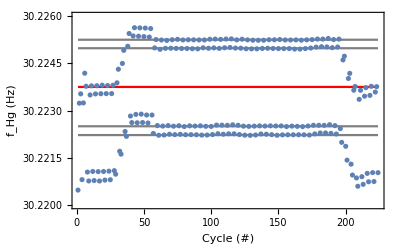

```mathematica
Show[{
Plot[{30.22375,30.22498,30.22525,30.2225,30.22222},{x,1,maxCy},PlotStyle->{Red,Gray,Gray,Gray,Gray},PlotRange->{{1,maxCy},{30.220,30.226}},Frame->True,FrameLabel->{"Cycle (#)","f_Hg (Hz)"},ImageSize->{1000},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},Axes->None]
,
EDAListPlot[data[[;;,-1]],Frame->True,FrameLabel->{"Cycle (#)","f_Hg (Hz)"},ImageSize->{1000},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black}]
}]
```

```mathematica
EDAListPlot[data[[;;,-13]],Frame->True,FrameLabel->{"Cycle (#)","f_Hg (Hz)"},ImageSize->{1000},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black}]
```

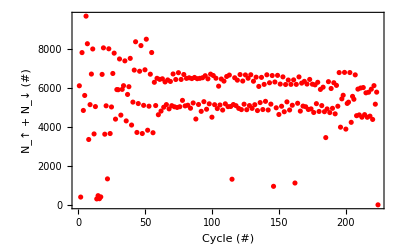

```mathematica
Show[{
EDAListPlot[Table[{k,{data[[;;,27]][[k]],Sqrt[data[[;;,27]][[k]]]}},{k,1,maxCy}],PlotStyle->Red,Frame->True,FrameLabel->{"Cycle (#)","N_↑ + N_↓ (#)"},ImageSize->{1000},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black}]
}]
```

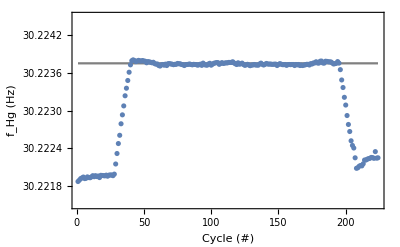

```mathematica
Show[{
Plot[{30.22375},{x,1,maxCy},PlotStyle->{Red,Gray,Gray,Gray,Gray},PlotRange->{{1,maxCy},{30.2215,30.2245}},Frame->True,FrameLabel->{"Cycle (#)","f_Hg (Hz)"},ImageSize->{1000},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},Axes->None]
,
EDAListPlot[data[[;;,-5]]*3.842435,Frame->True,FrameLabel->{"Cycle (#)","f_Hg (Hz)"},ImageSize->{1000},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black}]
}]
```

## Extras

```mathematica
nlm["ParameterPValues"]
(x/.Solve[(1-CDF[ChiSquareDistribution[2],x])==nlm["EstimatedVariance"],x][[1]][[1]])
```

{0.00290914,6.23945×10^-14}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

16.8692

```mathematica
nlm["AdjustedRSquared" ]
nlm["AIC"]
nlm["AICc"]
nlm["BIC"]
nlm["RSquared"]
```

0.988527

-19.1595

∞

-21.0006

0.994263